```mathematica
Clear["Global`*"]
```

# Parameters

```mathematica
Subscript[ρ, max]=1 (*maximum carbon uptake rate (d^-1)*);
Subscript[α, max]=1.5*10^-9(*attack rate of mixotroph on bacteria (cm^2*d^-1*Subscript[cell, M]^-1)*);
b=.15(*conversion rate of bacteria to mixotroph (Subscript[cell, M]*Subscript[cell, B]^-1)*);
Subscript[K, B]=1 10^8; (*carrying capacity of bacteria (Subscript[cell, B]*cm^-2)*);
r=.3(*growth rate of bacteria (d^-1)*);
h=250(*half saturation constant for photosynthesis (µmol quanta*m^2*s^-1)*);
Subscript[I, in]=100(*incident light (µmol quanta*m^2*s^-1)*);
k=5*10^(-7)(*mixotroph light absorbance constant (cm^2*Subscript[cell, M]^-1)*);
l=.05(*mixotroph mortality rate (d^-1)*);
Subscript[m, ρ]=.1;(*photosynthetic temeprature sensitivity coefficient (^o C^-1)*);
Subscript[m, α]=.25;(*heterotrophic temperature sensitivity coefficient (^o C^-1)*);
T0=13; (*baseline temperature (^o C)*);
T0α=T0 - 1/Subscript[m, α] (*minmimum temperature for heterotrophy (^o C)*);
T0ρ=T0 - 1/Subscript[m, ρ] (*minmimum temperature for photosynthesis (^o C)*);
```

# Equations/Functions for generating outputs

## Equations

```mathematica
(*temperature-dependent photosynthetic rate*)
ρ[θ_,z_,T_]:=Subscript[ρ, max]*(1-θ^(2^z))^(1/2^z)(Subscript[m, ρ] (T-T0ρ))

(*temperature-dependent grazing rate*)
α[θ_,T_]:=Subscript[α, max]*θ (Subscript[m, α] (T-T0α))

(*solves for mixotroph and bacteria population density at equilibrium*)
eqs[θ_,z_,T_]:=FindRoot[{dM[θ, z,T] ==0,dB[θ,T]==0 },{{M,10^7},{B,10^7}}]

(*mixotroph per capita  growth rate*)
dM[θ_, z_,T_]:=(ρ[θ,z,T]/(k M) Log[(h+Subscript[I, in])/(h+Subscript[I, in]* Exp[-k M ])]-l+ α[θ,T] b B) 

(*bacteria per capita growth rate*)
dB[θ_,T_]:=(r(1-(B/Subscript[K, B]))-α[θ,T]  M) 

(*mutant fitness equation*)
Fitness[θm_,z_,M_,B_,T_]:=-l+α[θm,T]  b B +(ρ[θm,z,T] Log[(h+Subscript[I, in])/(h+ ⅇ^(-(k M)) Subscript[I, in])])/(k M)

(*selection gradient*)
SelectionGrad[θm_,z_,M_,B_,T_]:=Subscript[α, max] (1+Subscript[m, α] (T-T0)) b B -(ρ[θm,z,T] θm^(-1+2^z) (1-θm^(2^z))^-1  Log[(h+Subscript[I, in])/(h+ⅇ^(-k M) Subscript[I, in])])/(k M)
```

## Pairwise invasibility plots (PIP)

```mathematica
(*Uses a chosen shape parameter z, temperature T, and color to generate a pairwise invasibility plot using the fitness function for an invading mutant mixotroph. Regions in which mutant fitness is positive are shaded*)
MakePIP[z_,T_,color_]:=RegionPlot[Fitness[θm,z,M/.eqs[θ,z,T],B/.eqs[θ,z,T],T]≥  0,{θ,0,1},{θm,0,1},PlotStyle->color,BoundaryStyle->{Bold,Dashed,Black},Frame->True,FrameLabel->{Style["θ_res",12,Black],Style["θ_mut",12,Black]},FrameTicksStyle->Directive[Black,12]]
```

## Generating ESS vs Temp plots for generalist and specialist mixotrophs

```mathematica
(*makeListGen[] and makeListLin[] generate lists containing the evolutionarily stable investment strategy Subscript[θ, ESS] as a function of temperature for generalist tradeoff and linear tradeoff mixotrophs respectively*)
```

```mathematica
makeθListGen[]:=
{
θESSgen = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,1,M/.eqs[θm,1,T],B/.eqs[θm,1,T],T]==0,{θm,.99}];
If[Re[currentθ] > 1, AppendTo[θESSgen, 1],(*if calculated Subscript[θ, ESS] > 1 (maximum heterotrophic investment), 1 is added to list*)If[Re[currentθ] < 0, AppendTo[θESSgen,0.],AppendTo[θESSgen,currentθ]]](*if calculate Subscript[θ, ESS] < 0 (minimum heterotrophic investment), 0 is added to list*)
]];
θESSgen
}
makeθListLin[]:=
{
θESSlin = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,0,M/.eqs[θm,0,T],B/.eqs[θm,0,T],T]==0,{θm,.5}];
(*getting around issue where FindRoot identifies the incorrect, evolutionarily unstable root in some cases*)
If[1/(.0001)(SelectionGrad[.0002,0,M/.eqs[.0002,0,T],B/.eqs[.0002,0,T],T]-SelectionGrad[.0001,0,M/.eqs[.0001,0,T],B/.eqs[.0001,0,T],T]) > 0,AppendTo[θESSlin,1],If[Re[currentθ] > 1, AppendTo[θESSlin, 1],If[Re[currentθ] < 0, AppendTo[θESSlin,0.000],AppendTo[θESSlin,currentθ]]]]
]];
θESSlin 
}
```

## Comparing evolved vs unevolved mixotrophs for carbon cycling

```mathematica
(*generates plots comparing mixotroph and bacteria populations, and growth rate components derived from photosynthesis, P(θ,z,I,T,M^*), and heterotrophy, G(θ,T,B^*), between evolving mixotrophs whos heterotrophic investment θ varies as a function of temperature and genetically static mixotrophs with fixed θ. This allows evolutionary and strictly thermal responses to be compared. Function inputs consist of the shape parameter, z, the chosen lower bounds for each set of plots (l1, l2, and l3) and the chosen upper bounds for each set of plots (u1, u2, and u3)*)
Ccycling[z_,l1_,u1_,l2_,u2_,l3_,u3_]:=
{makeθListLin[];
makeθListGen[];
θList=List[];
If[z ==0,θList=θESSlin,θList=θESSgen];

Mpopsevo=List[];
Mpopsnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsevo,M/.eqs[θList[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsnoevo,M/.eqs[θList[[T0]],z,t]]]];

bpopsevo=List[];
bpopsnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsevo,B/.eqs[θList[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsnoevo,B/.eqs[θList[[T0]],z,t]]]];

photgrowthevo=List[];
photgrowthnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthevo,(M/.eqs[θList[[t]],z,t])*((ρ[θList[[t]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList[[t]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList[[t]],z,t])))]]];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthnoevo,(M/.eqs[θList[[T0]],z,t])*((ρ[θList[[T0]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList[[T0]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList[[T0]],z,t])))]]];


hetgrowthevo=List[];
hetgrowthnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthevo,(B/.eqs[θList[[t]],z,t])*(M/.eqs[θList[[t]],z,t]) α[θList[[t]],t] b]]];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthnoevo,(B/.eqs[θList[[T0]],z,t])*(M/.eqs[θList[[T0]],z,t]) α[θList[[T0]],t] b]]];


List[ListPlot[{Mpopsevo,Mpopsnoevo},Joined->True,PlotRange->{{T0,18},{l1, u1}},PlotStyle->{{Black},{Black,Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["M^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{bpopsevo,bpopsnoevo},Joined->True,PlotRange->{{T0,18},{l2, u2}},PlotStyle->{{Black},{Black,Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["B^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{photgrowthevo,photgrowthnoevo,hetgrowthevo,hetgrowthnoevo},Joined->True,PlotRange->{{T0,18},{l3, u3}},PlotStyle->{{Darker[Green]},{Darker[Green],Dashed},{Black},{Black,Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",Black,15], Style["P(θ,z,I,T,M^*)*M, G(θ,T,B^*)*M",Black,12]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]]
}
```

# θ vs. Temperature plots

## I_in=100

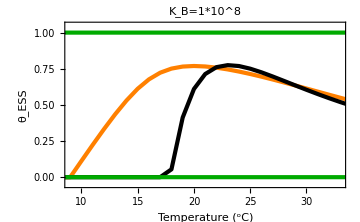
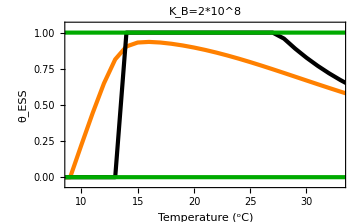
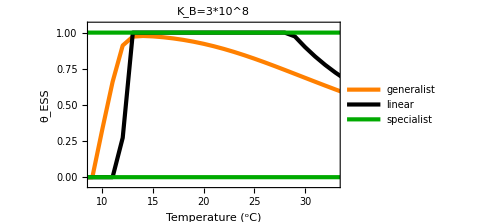

```mathematica
ones=Table[1,100];
zeros=Table[0,100];
List[Subscript[K, B]=1 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["θ_ESS",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=1*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["θ_ESS",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["θ_ESS",12,Black]},PlotLegends->{"generalist", "linear","specialist"},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

## I_in=150

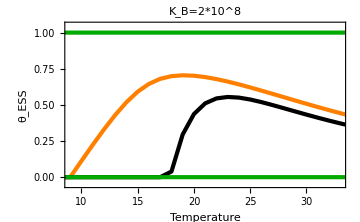
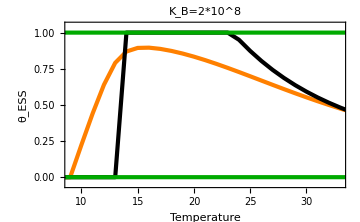
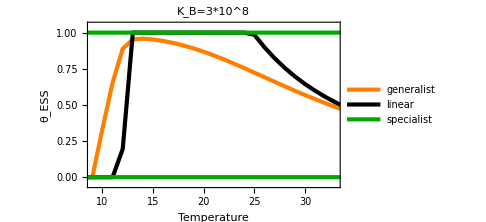

```mathematica
ones=Table[1,100];
zeros=Table[0,100];
List[Subscript[K, B]=1 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature",15,Black],Style["θ_ESS",15,Black]},FrameTicksStyle->Directive[Black,15],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature",15,Black],Style["θ_ESS",15,Black]},FrameTicksStyle->Directive[Black,15],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,ones,zeros},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{Orange,AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]},{Darker[Green],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature",15,Black],Style["θ_ESS",15,Black]},FrameTicksStyle->Directive[Black,15],PlotLegends->{"generalist", "linear","specialist"},PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

# Pairwise invasibility plots

## K_B=1*10^8, I_in=100

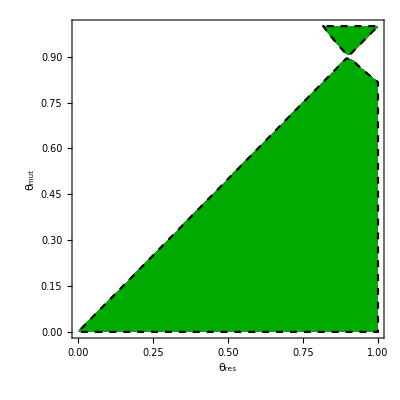
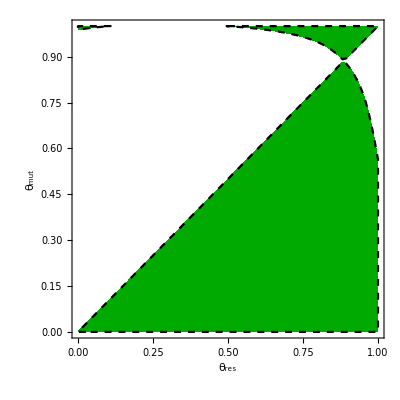
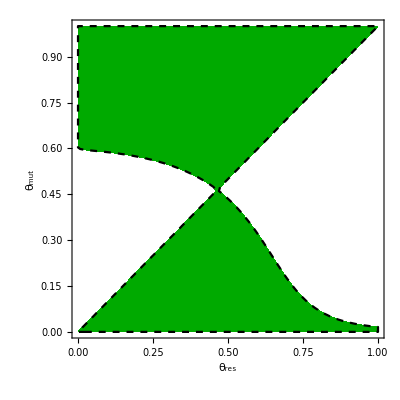

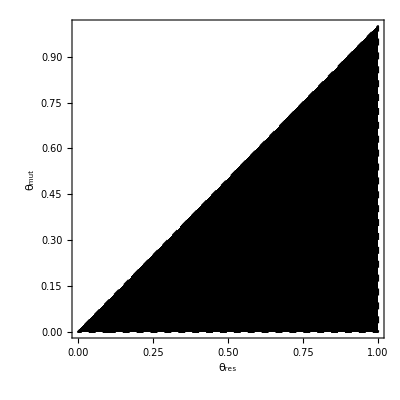
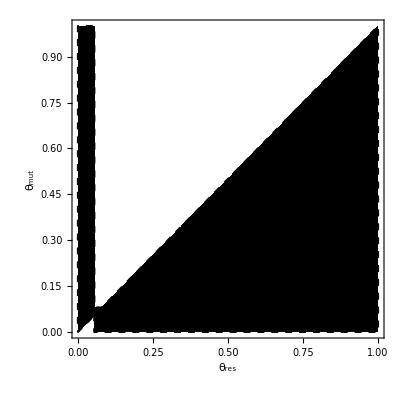
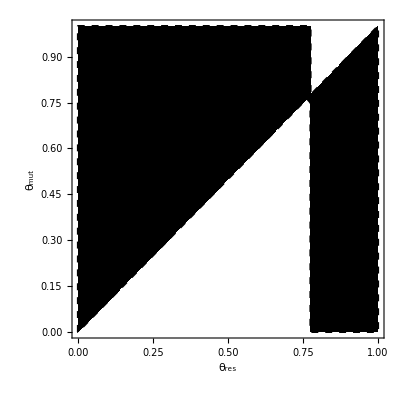

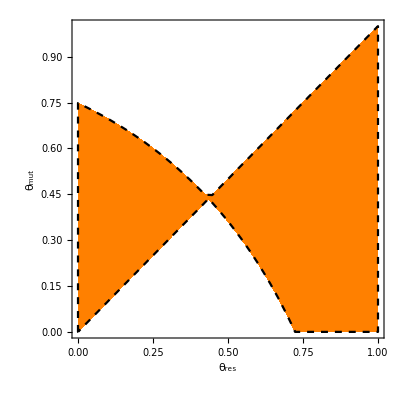
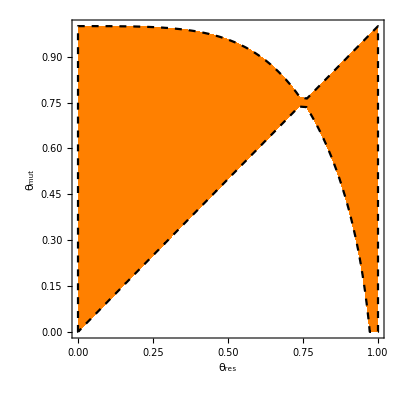

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=100;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

## K_B=2*10^8, I_in=100

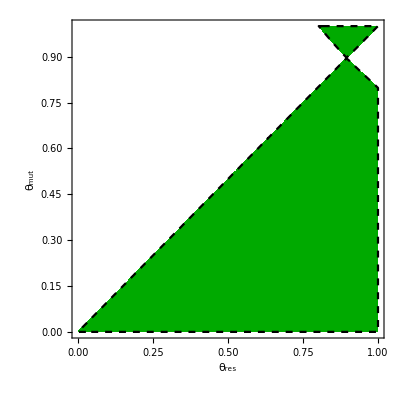
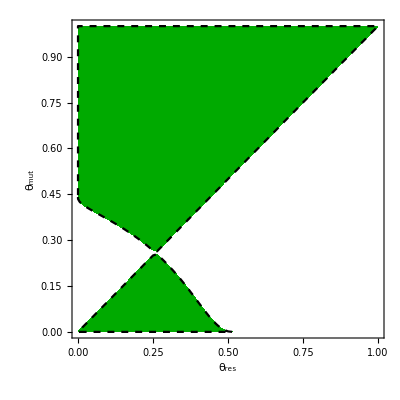
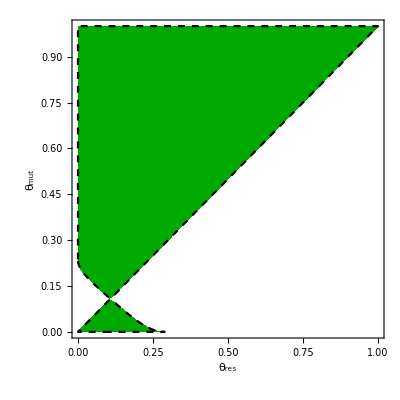

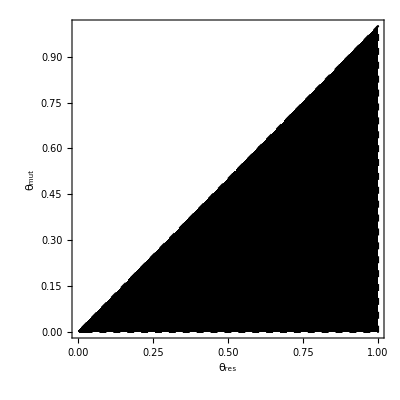
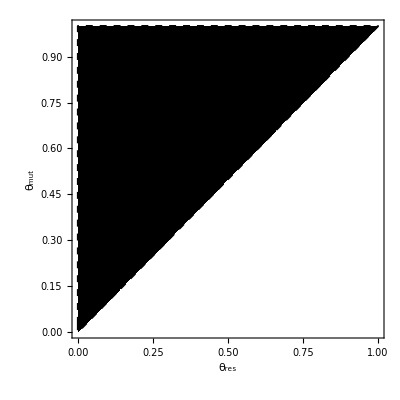
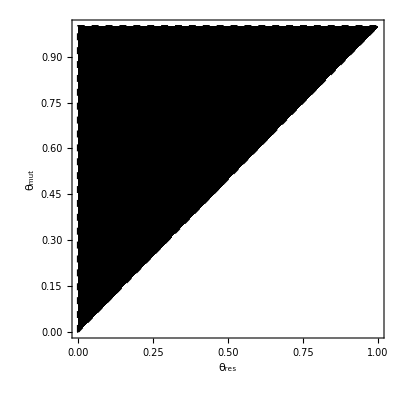

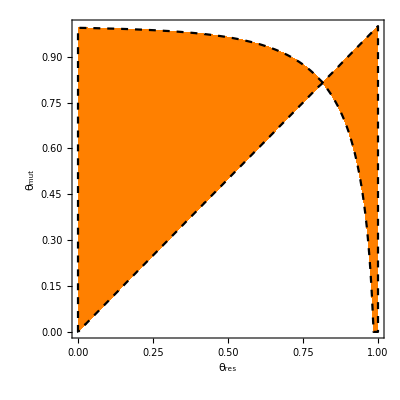
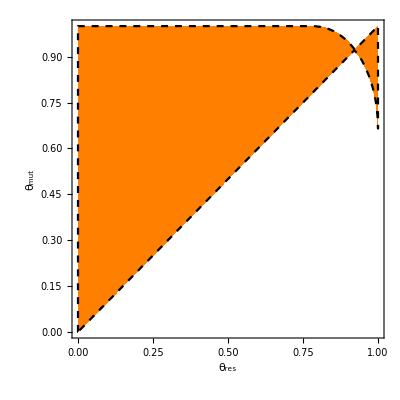

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=100;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

## K_B=3*10^8, I_in=100

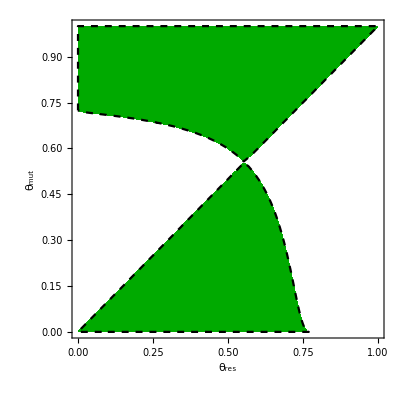
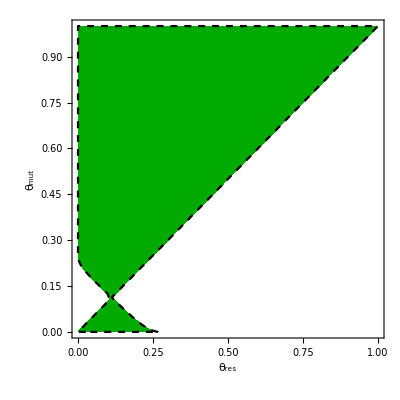
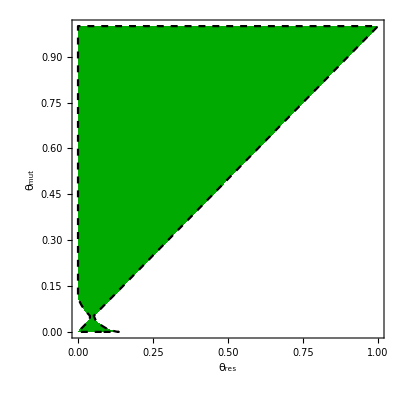

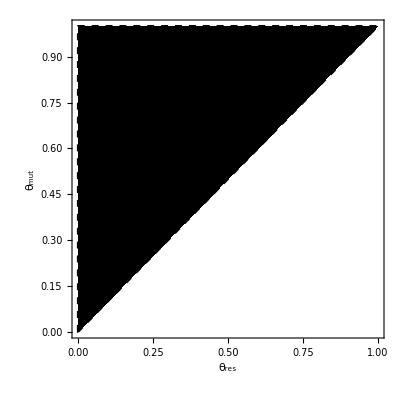
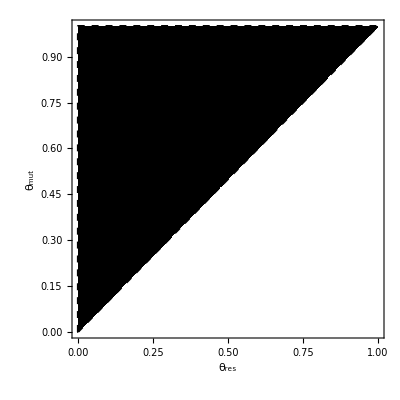
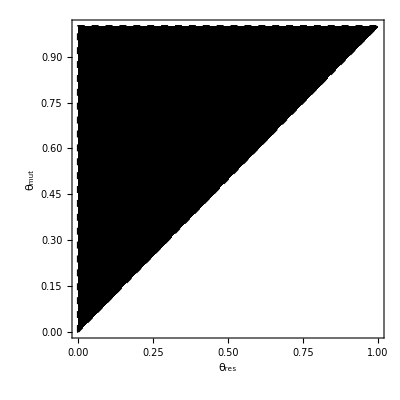

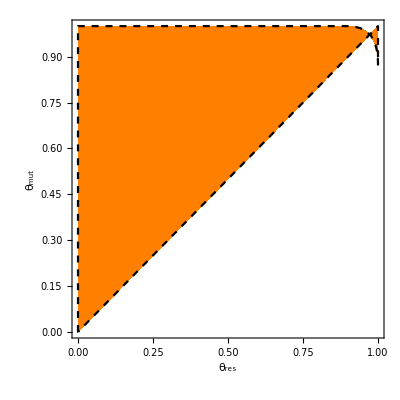
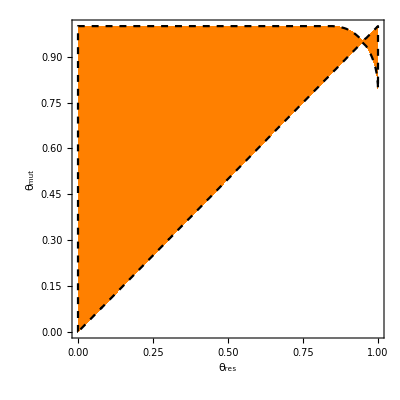

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=100;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

## K_B=1*10^8, I_in=150

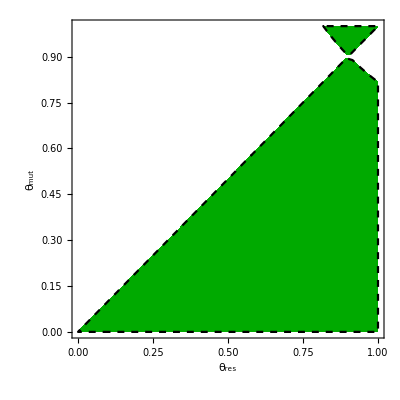
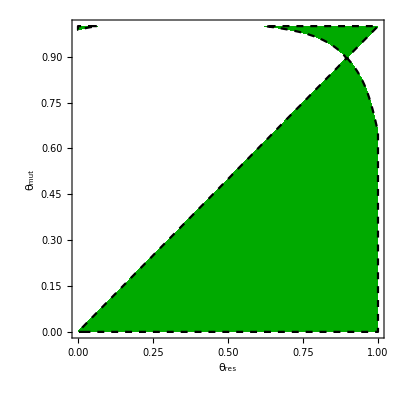
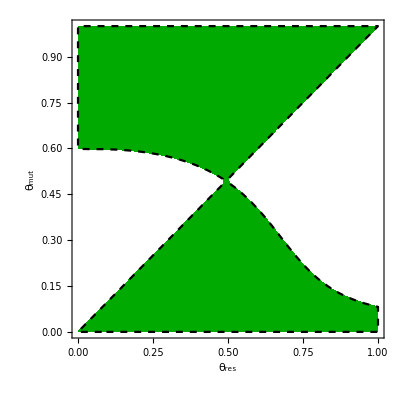

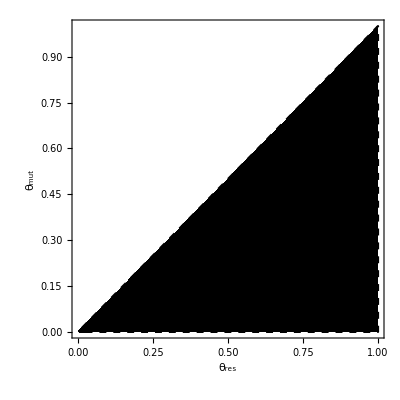
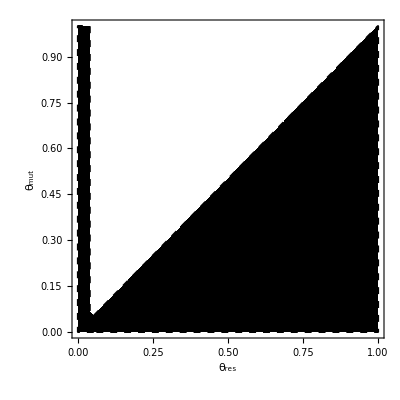
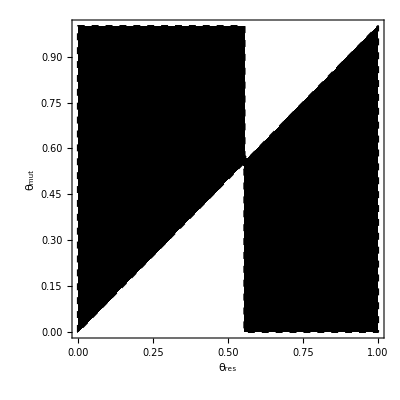

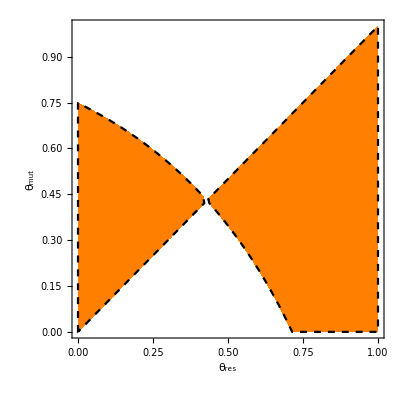
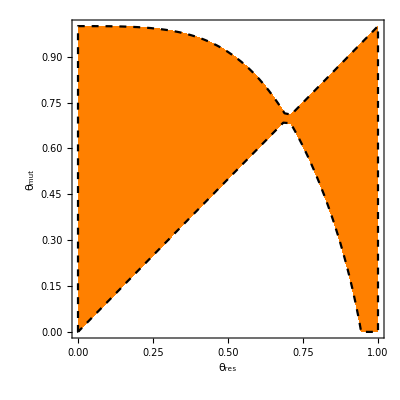

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=150;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

## K_B=2*10^8, I_in=150

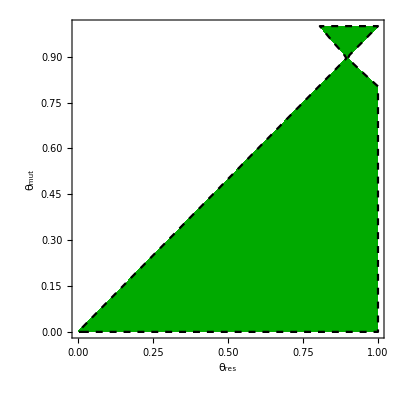
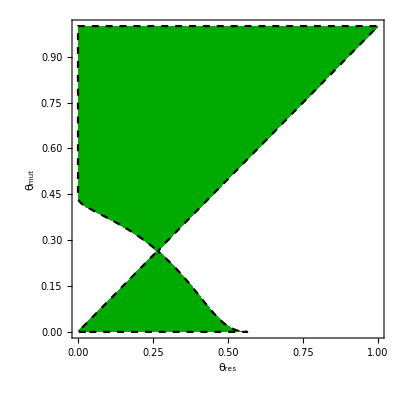
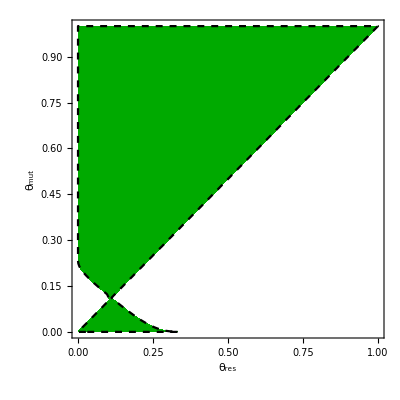

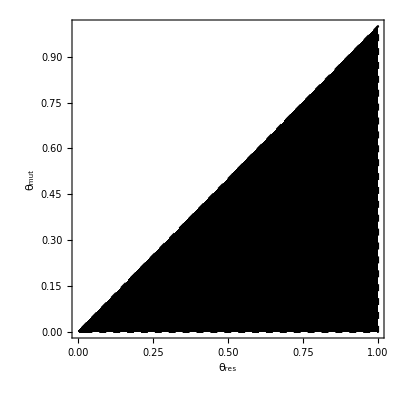
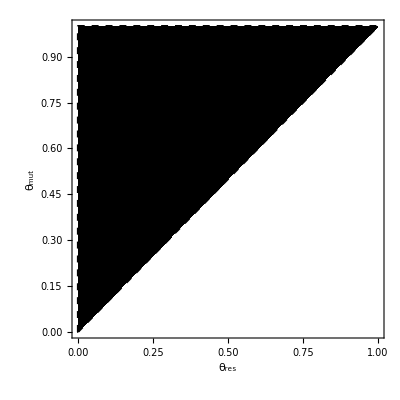
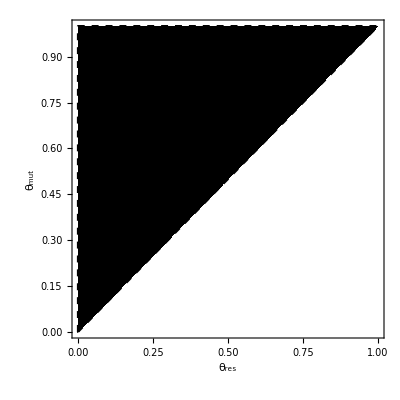

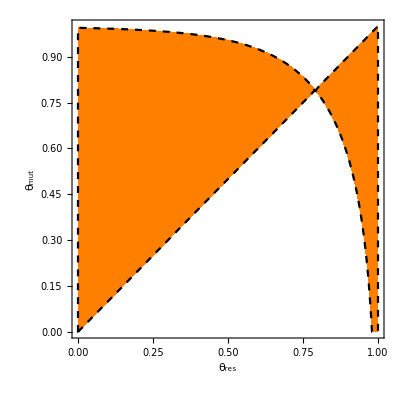
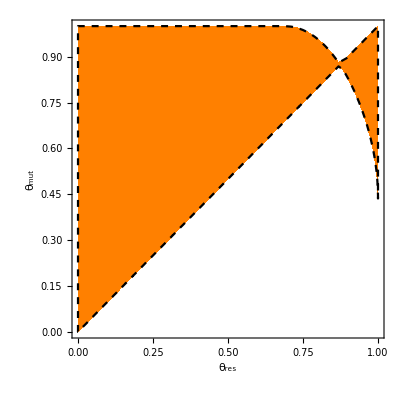

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=150;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

## K_B=3*10^8, I_in=150

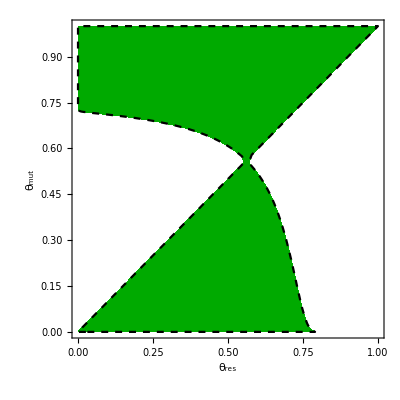
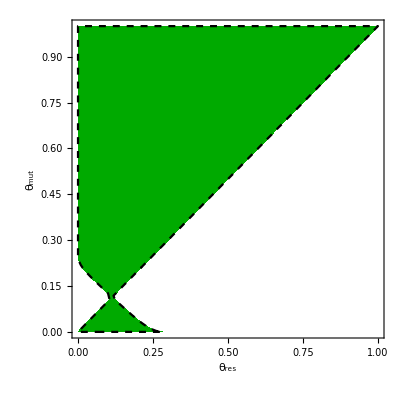
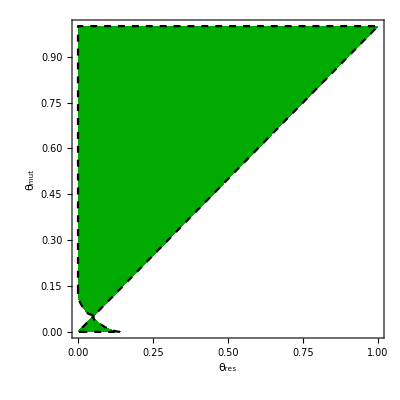

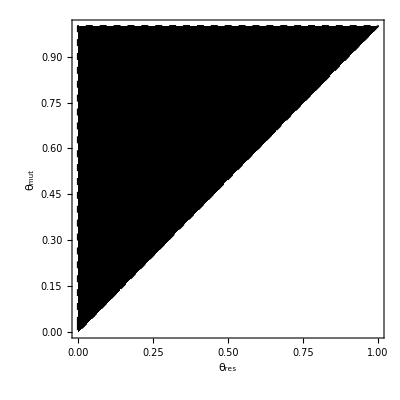
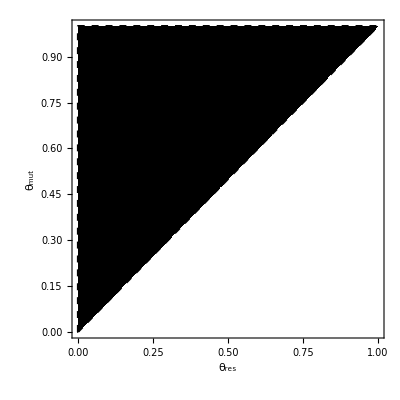
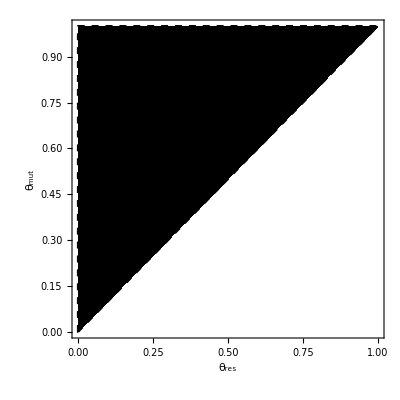

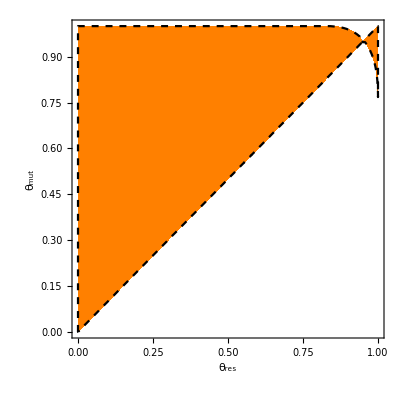
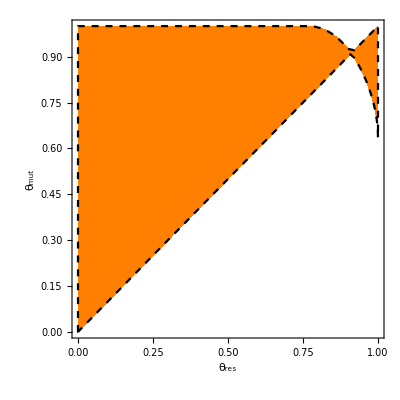

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=150;
Quiet[List[MakePIP[-1,T0,Darker[Green]],MakePIP[-1,T0+5,Darker[Green]],MakePIP[-1,T0+10,Darker[Green]]]](*specialist*)
Quiet[List[MakePIP[0,T0,Black],MakePIP[0,T0+5,Black],MakePIP[0,T0+10,Black]]] (*linear*)
Quiet[List[MakePIP[1,T0,Orange],MakePIP[1,T0+5,Orange],MakePIP[1,T0+10,Orange]]](*generalist*)
```

# C-cycling related figures (Dashed - genetically static, Solid - evolving)

## K_B=1*10^8, I_in=100

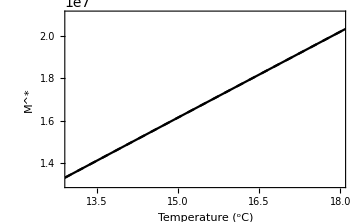
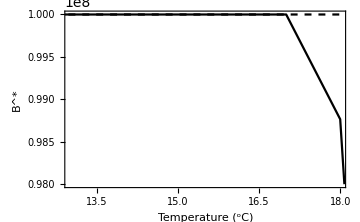
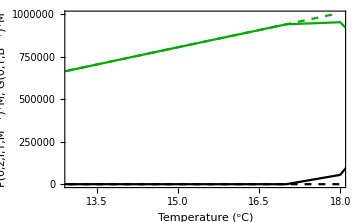

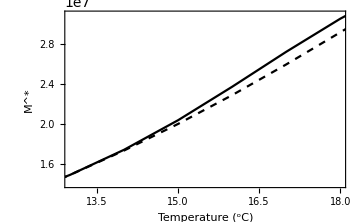
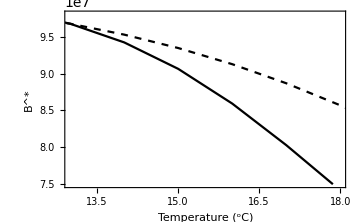
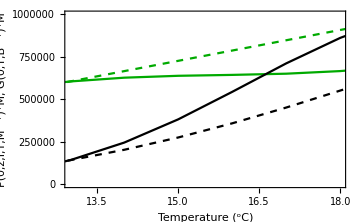

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=100;
Quiet[Ccycling[0,1.3 10^7,2.1 10^7 ,9.8 10^7,1 10^8,0,1 10^6]]
Quiet[Ccycling[1,1.4 10^7,3.1 10^7 ,7.5 10^7,9.8 10^7,0,1 10^6]]
```

## K_B=2*10^8, I_in=100

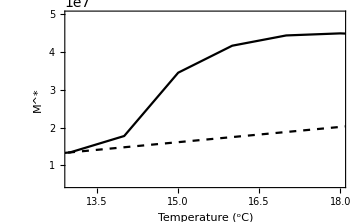
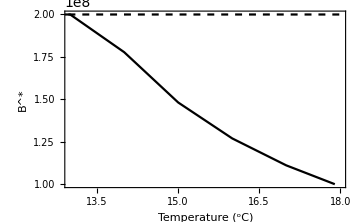
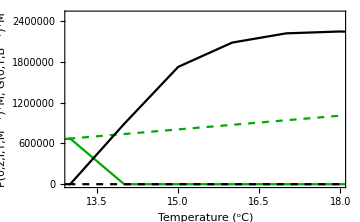

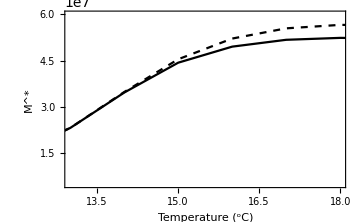
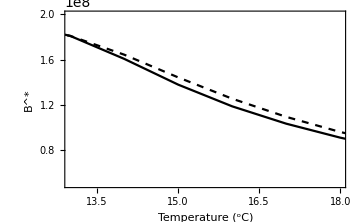
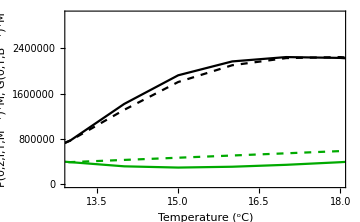

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=100;
Quiet[Ccycling[0,.5 10^7,5 10^7 ,1.0 10^8,2 10^8,0,2.5 10^6]]
Quiet[Ccycling[1,.5 10^7,6 10^7 ,5 10^7,2 10^8,0,3 10^6]]
```

## K_B=3*10^8, I_in=100

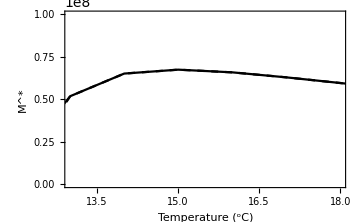
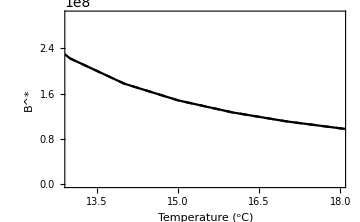
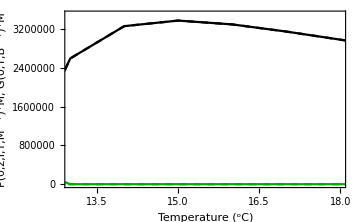

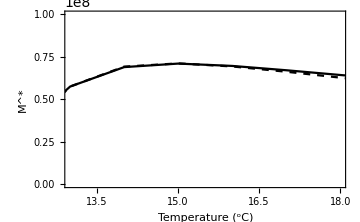
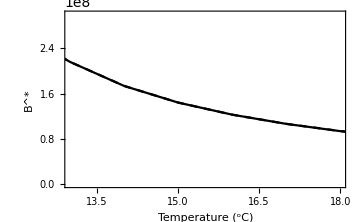
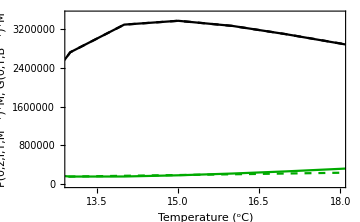

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=100;
Quiet[Ccycling[0,0 10^7,1 10^8 ,0 10^7,3 10^8,0,3.5 10^6]]
Quiet[Ccycling[1,0 10^7,1 10^8 ,0 10^7,3 10^8,0,3.5 10^6]]
```

## K_B=1*10^8, I_in=150

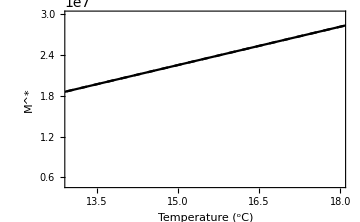
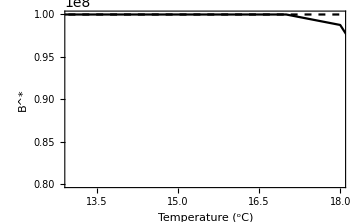
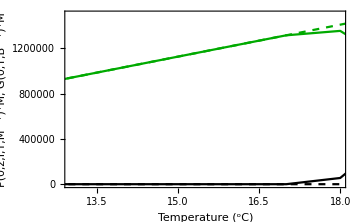

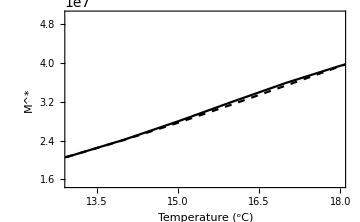
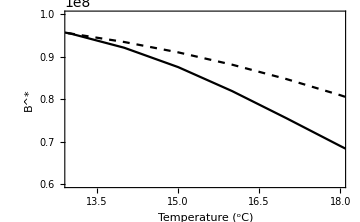
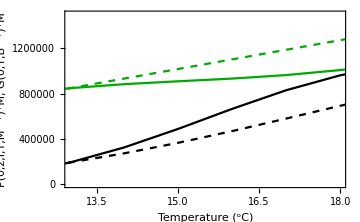

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=150;
Quiet[Ccycling[0,.5 10^7,3.0 10^7 ,8 10^7,1 10^8,0,1.5 10^6]]
Quiet[Ccycling[1,1.5 10^7,5 10^7 ,6 10^7,1 10^8,0,1.5 10^6]]
```

## K_B=2*10^8, I_in=150

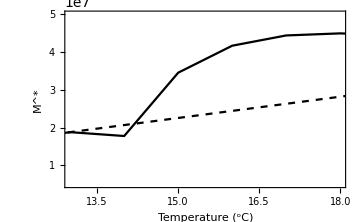
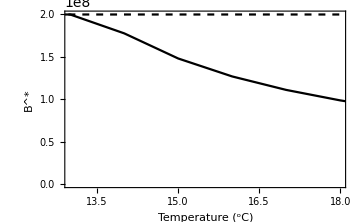
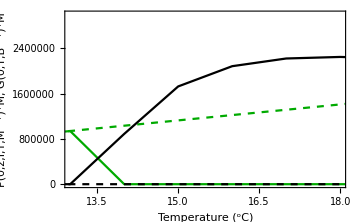

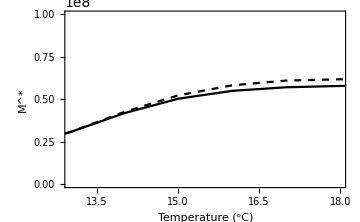
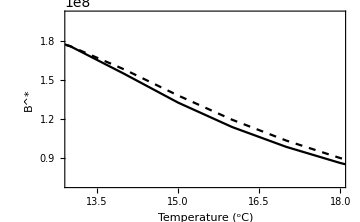
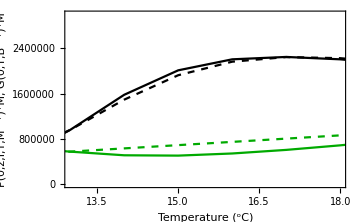

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=150;
Quiet[Ccycling[0,.5 10^7,5.0 10^7 ,0,2 10^8,0,3 10^6]]
Quiet[Ccycling[1,0 10^7,1 10^8 ,7 10^7,2 10^8,0,3 10^6]]
```

## K_B=3*10^8, I_in=150

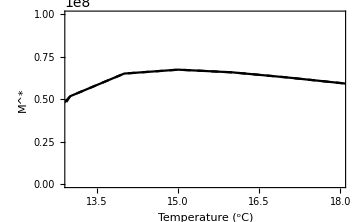
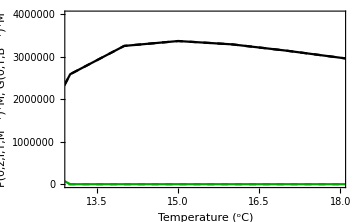
{{-Graphics-,-Graphics-,-Graphics-}}

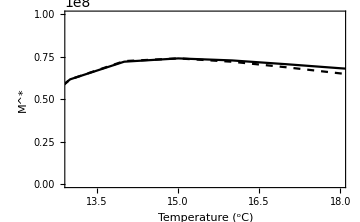
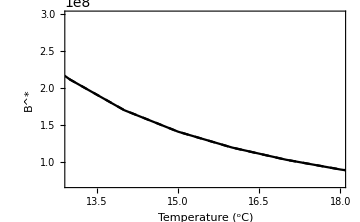
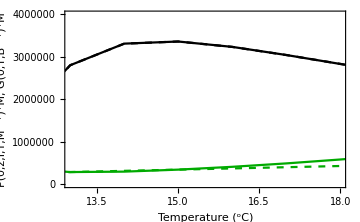

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=150;
Quiet[Ccycling[0,0 10^7,1.0 10^8 ,0 10^7,3 10^8,0,4 10^6]]
Quiet[Ccycling[1,0 10^7,1 10^8 ,7 10^7,3 10^8,0,4 10^6]]
```